## Kapitola 5 - Dopředná síť a Iris data

Demonstrace použití dopředné neuronové sítě na datech z databáze UCI.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

## Import dat

### Načtení dat ze souboru

Nastavíme si pracovní adresář na ten, kde máme uložen aktuální notebook, načítaná data musejí být ve stejném adresáři.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Dokumenty\ŠKOLA\ČVUT\BP\BP_Neuron

A načteme data.

```mathematica
data=Import["iris.data"];
```

### Načtení dat z internetu

Jiná možnost je importovat data přímo z internetu - příklad pro UCI databázi (stejná data jako při načítání ze souboru, jen načtena přímo z internetu.

```mathematica
data=Import["http://ftp.ics.uci.edu/pub/machine-learning-databases/iris/iris.data"];
```

## Předzpracování dat

V proměnné data máme uložen celý datový soubor. Můžeme se podívat kolik obsahuje vektorů.

```mathematica
Dimensions[data]
```

{151}

Je zde 151 vektorů. Protože ale datový soubor obsahuje prázdné řádky na konci, není to matice, ale "heterogenní" seznam. Můžeme se podívat ... následující příkaz zobrazí 5 posledních záznamů:

```mathematica
Take[data,-5]
```

{{6.3,2.5,5.,1.9,Iris-virginica},{6.5,3.,5.2,2.,Iris-virginica},{6.2,3.4,5.4,2.3,Iris-virginica},{5.9,3.,5.1,1.8,Iris-virginica},{}}

Vidíme, že na konci je prázdný záznam. Odstraníme ho a nová data si uložíme do proměnné "data2" - můžeme si přepsat i původní proměnnou "data" - na tom víceméně nezáleží. Přiřazením do nové proměnné se vyhneme případným problémům, kdybychom víckrát po sobě příkaz vyhodnotili (pokaždé by nám to "ukrojilo" poslední záznam).

```mathematica
data2=Drop[data,-1];
```

Zobrazíme si výsledek (posledních 10 zaznamů).

```mathematica
Take[data2,-10]
```

{{6.7,3.1,5.6,2.4,Iris-virginica},{6.9,3.1,5.1,2.3,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{6.8,3.2,5.9,2.3,Iris-virginica},{6.7,3.3,5.7,2.5,Iris-virginica},{6.7,3.,5.2,2.3,Iris-virginica},{6.3,2.5,5.,1.9,Iris-virginica},{6.5,3.,5.2,2.,Iris-virginica},{6.2,3.4,5.4,2.3,Iris-virginica},{5.9,3.,5.1,1.8,Iris-virginica}}

### Rozdělení dat na vstupní a výstupní vektory

Celý datový soubor si rozdělíme na množinu vstupních dat a množinu výstupních dat.

```mathematica
data2[[1]]
```

{5.1,3.5,1.4,0.2,Iris-setosa}

První 4 položky jsou vstupní hodnoty. Poslední (5.) je výstupní hodnota. Pro pochopení následujícího příkazu je potřeba "myslet maticově" - teď jsou data reprezentována seznamem, kde každý prvek je jeden vektor vstupu a výstupu (jeden řádek datového souboru) - pokud tento seznam transponujeme, dostaneme seznam, kde každý prvek bude reprezentovat hodnoty jednotlivých atributů - zaměníme sloupce a řádky. V transponovaném seznamu vybereme příslušné sloupce a po transponování zpět dostáváme zase vektory dat.

První 4 hodnoty jsou vstupní.

```mathematica
inData=Transpose[Take[Transpose[data2],4]];
(* 4 udává, že separujeme první 4 hodnoty *)
```

Protože jako výstupní hodnoty vybíráme data na zadaném indexu, je potřeba ho napsat do složených závorek {5} - syntaktická záležitost. Dalo by se také použít "Take[..., -1]" - jeden (obecně n) prvek od konce.

```mathematica
outDataTmp=Transpose[Take[Transpose[data2],{5}]];
```

### Vlastní předzpracování - překódování dat

V datech jsou textové atributy, které je pro potřeby klasifikace dopřednou sítí nutné překódovat. Použijeme kód "1 z N".

```mathematica
Take[outDataTmp,5]
```

{{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa}}

Protože se nám nechce zadávat ručně kódovací tabulku a navíc chceme mít univerzální řešení, vytvoříme kódovací tabulku automaticky.

Prvním krokem je zjistit jaký je obor hodnot textového (výstupního) atributu. Funkcí "Flatten" - zrušíme hierarchii v seznamu - teď jsou výstupní data uložena jako seznam, kde každý prvek je seznam o jedné hodnotě. Uděláme z něj tedy jednoúrovňový seznam.

Příklad pro pochopení :

```mathematica
(* Ukázka původních dat *)
Take[outDataTmp,5] 
(* Ukázka "srovnaných" dat *)
Take[Flatten[outDataTmp],5]
```

{{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa}}

Data tedy srovnáme funkcí "Flatten" a potom seřadíme funkcí "Sort". Na tento seznam použijeme funkci "Split", která nam zadaný seznam (v našem případě seřazený seznam výstupních hodnot) rozdělí na seznamy podle funkční hodnoty - pokud jsou tedy v datech celkem 3 různé hodnoty, jsou ve výsledku vytvořeny 3 seznamy - každý obsahuje prvky s jednou hodnotou.

Pro lepší pochopení si zkuste vyhodnotit následující příkazy (celý postup rozfázovaný do jednotlivých kroků). POZOR - výstupy mohou být dost veliké (zobrazuje se celý soubor dat).

```mathematica
outDataTmp
```

{{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-setosa},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-versicolor},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica},{Iris-virginica}}

```mathematica
Flatten[outDataTmp]
```

{Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica}

```mathematica
Sort[Flatten[outDataTmp]]
```

{Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica}

```mathematica
Split[Sort[Flatten[outDataTmp]]]
```

{{Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa,Iris-setosa},{Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor,Iris-versicolor},{Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica,Iris-virginica}}

Teď máme tolik seznamů, kolik je různých hodnot výstupů - z každého tohoto seznamu tedy vezmeme první prvek jako reprezentanta. Uděláme to namapovaním funkce "First" (vrací první prvek zadaného seznamu).

```mathematica
outVal=First[#]&/@Split[Sort[Flatten[outDataTmp]]]
```

{Iris-setosa,Iris-versicolor,Iris-virginica}

V proměnné "outVal" teď máme obor hodnot výstupu.

Vytvoříme převodní tabulku. MapIndexed funguje stejně jako Map, ale v druhém parametru (#2) předává index prvku, na který je funkce aktuálně mapována. SparseArray slouží k vytváření tzv. řídkých matic - zde ji použijeme jako nástroj pro jednoduché vytvoření výsledného vektoru. Chceme totiž nulový vektor s jedničkou pouze na jedné pozici.

Příklad :

```mathematica
SparseArray[3->1] (* Na pozici 3 bude hodnota 1 *)
```

SparseArray[<1>,{3}]

```mathematica
Normal[%] (* Řídkou matici převedeme na normální *)
```

{0,0,1}

Vidíme, že to je přesně to, co chceme, takže teď aplikujeme tento příkaz na celý seznam výstupních hodnot, uložených v proměnné "outVal".

```mathematica
encode=MapIndexed[#1->Normal[SparseArray[#2->1,{Length[outVal]}]]&,outVal]
```

{Iris-setosa→{1,0,0},Iris-versicolor→{0,1,0},Iris-virginica→{0,0,1}}

Proměnná "encode" teď obsahuje seznam tzv. přepisovacích pravidel - vidíme, že každé textové hodnotě je přiřazen jeden vektor.

Pomocí konstrukce "/." můžeme tato přepisovací pravidla aplikovat na původní data a získáme tak zakódovaná data.

Příklad pro pochopení (znak šipky se zadává jako "pomlčka" a "většítko" tj. "-" a ">"):

```mathematica
{a,b,c}/.{a->1,b->2,c->3} (* "a" kódujeme jako "1", "b" jako "2", atd.*)
```

{1,2,3}

Další příklad :

```mathematica
{a,b,c}/.{a->{1,0,0},b->{0,1,0},c->{0,0,1}}
```

{{1,0,0},{0,1,0},{0,0,1}}

Teď už můžeme konečně zakódovat naše data.

Zjištění, zda jsou některé výstupní hodnoty textové - pokud ano, provede se překódováni do "1 z N".

```mathematica
outData=Flatten[outDataTmp]/.encode;
```

Jak to vypadá? Koukneme se :

```mathematica
Take[outData,5]
```

{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0}}

## Jednoduché zpracování dat neuronovou sítí

Inicializace sítě - zadáme trénovací množinu, počet neuronů, případně můžeme zadat i aktivační funkci neuronu. Počet neuronů se zadává jako seznam, každý prvek (číslo) seznamu odpovídá počtu neuronů v jedné vrstvě. {5} znamená jedna skrytá vrstva s pěti neurony. {4,3} znamená dvě skryté vrstvy, jedna se čtyřmi neurony a druhá se třemi neurony.

Vytvořenou síť si uložíme do proměnné "net".

```mathematica
net=InitializeFeedForwardNet[inData,outData,{3,2},Neuron->Sigmoid]
```

FeedForwardNet[{{w1,w2,w3}},{Neuron → Sigmoid, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 5, 3, 15, 59, 44.842683}, OutputNonlinearity → None, NumberOfInputs → 4}]

Můžeme si nechat zobrazit podrobnější informace o vytvořené síti.

```mathematica
NetInformation[net]
```

FeedForward network created 2011-5-3 at 15:59. The network has 4 inputs and 3 outputs. It consists of 2 hidden layers with number of neurons per layer given by {3, 2}. The neuron activation function is of Sigmoid type.

Teď síť natrénujeme pomocí funkce "NeuralFit", které zadáme naší síť (proměnná "net"), trénovací množinu ("inData" a "outData") a počet učících kroků.

Funkce NeuralFit vyprodukuje naučenou síť a záznam o průběhu učení (může se hodit) - obě tyto návratové hodnoty si ukládáme (do proměnné "net2" a "record").

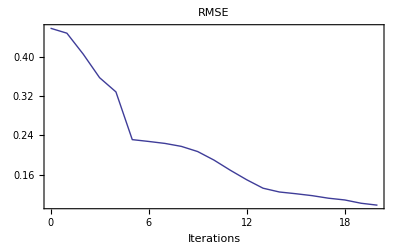

```mathematica
{net2,record}=NeuralFit[net,inData,outData,20];
```

Máme síť naučenou a můžeme se podívat například na to, jak odpovídala během učení. Síť má 3 výstupy, proto následující příkaz vyprodukuje 3 grafy. Grafy zobrazují vývoj dobře a špatně klasifikovaných instancí jednotlivých tříd, pro každou třídu je jeden graf.

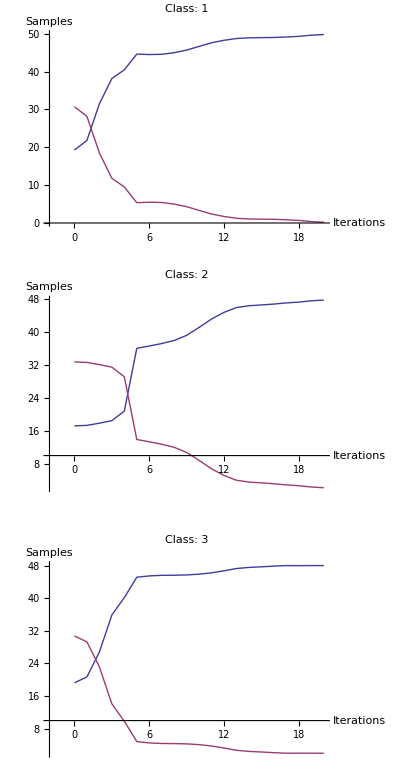

```mathematica
NetPlot[record,inData,outData,DataFormat->ClassPerformance]
```

Můžeme se podívat na klasifikaci pomocí "data/model" diagramu. Graf je interaktivní - pomocí myši ho můzeme otáčet, posouvat (Shift + myš) a zoomovat (Ctrl + myš). Čím více prvků je na diagonále, tím lépe.

```mathematica
NetPlot[net2,inData,outData,DataFormat->BarChart]
```

-Graphics3D-

Síť je možné si nechat symbolicky vyhodnotit - pro větší sítě je to ale už zcela nepřehledné, nicméně aktivační funkce tam zcela jistě poznáte.

Síť funguje v Mathematice jako klasická funkce, takže ji můžeme dávat parametry - včetně symbolů:

```mathematica
net2[{x1,x2,x3,x4}]
```

{-0.0113067+1.93327/(1+ⅇ^(1.98063-0.790317/(1+ⅇ^(-31.8407+7.70558 x1-0.482973 x2+3.76694 x3-4.06278 x4))+5.48283/(1+ⅇ^(-35.4643+5.21425 x1+9.67668 x2-6.03418 x3-2.22728 x4))-2.07975/(1+ⅇ^(-11.2645-1.48646 x1-2.03974 x2+3.7374 x3+5.15584 x4))))+0.0117766/(1+ⅇ^(-1.09448+7.35464/(1+ⅇ^(-31.8407+7.70558 x1-0.482973 x2+3.76694 x3-4.06278 x4))-1.09385/(1+ⅇ^(-35.4643+5.21425 x1+9.67668 x2-6.03418 x3-2.22728 x4))+6.606/(1+ⅇ^(-11.2645-1.48646 x1-2.03974 x2+3.7374 x3+5.15584 x4)))),1.03999-1.97951/(1+ⅇ^(1.98063-0.790317/(1+ⅇ^(-31.8407+7.70558 x1-0.482973 x2+3.76694 x3-4.06278 x4))+5.48283/(1+ⅇ^(-35.4643+5.21425 x1+9.67668 x2-6.03418 x3-2.22728 x4))-2.07975/(1+ⅇ^(-11.2645-1.48646 x1-2.03974 x2+3.7374 x3+5.15584 x4))))-1.18053/(1+ⅇ^(-1.09448+7.35464/(1+ⅇ^(-31.8407+7.70558 x1-0.482973 x2+3.76694 x3-4.06278 x4))-1.09385/(1+ⅇ^(-35.4643+5.21425 x1+9.67668 x2-6.03418 x3-2.22728 x4))+6.606/(1+ⅇ^(-11.2645-1.48646 x1-2.03974 x2+3.7374 x3+5.15584 x4)))),-0.0286877+0.0462372/(1+ⅇ^(1.98063-0.790317/(1+ⅇ^(-31.8407+7.70558 x1-0.482973 x2+3.76694 x3-4.06278 x4))+5.48283/(1+ⅇ^(-35.4643+5.21425 x1+9.67668 x2-6.03418 x3-2.22728 x4))-2.07975/(1+ⅇ^(-11.2645-1.48646 x1-2.03974 x2+3.7374 x3+5.15584 x4))))+1.16875/(1+ⅇ^(-1.09448+7.35464/(1+ⅇ^(-31.8407+7.70558 x1-0.482973 x2+3.76694 x3-4.06278 x4))-1.09385/(1+ⅇ^(-35.4643+5.21425 x1+9.67668 x2-6.03418 x3-2.22728 x4))+6.606/(1+ⅇ^(-11.2645-1.48646 x1-2.03974 x2+3.7374 x3+5.15584 x4))))}

V následujícím notebooku si ukážeme podrobnější vyhodnocení výstupu neuronové sítě a také jiný přístup k učení sítě.

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury "Demonstrační aplikace pro podporu kurzu neuronových sítí" na FEL ČVUT 2011. Vznikl úpravou textu Petra Chlumského.